# f.figure.series-full.rencon3.strange.baryons-all.band.nb

## initial 1

```mathematica
(*计算环境参量，比如路径*)
gitRemoteName="octet.formfactor";(*给出远程git仓库的名字*)
cmdQ=Not[$Notebooks];(*脚本的运行模式判断，True代表命令行，False代表前端*)
fileName=If[Not[cmdQ],NotebookFileName[],$InputFileName](*给出笔记本的绝对路径*)
(*定义一些常用的函数*)
enList[x__]:=Replace[{x},{{y__}}:>{y},{0}](*定义一个确保列表的函数*)
enString[x__]:=StringJoin[ToString[#1]&/@enList[x]](*定义一个确保字符串的函数*)
If[cmdQ,
echo[x__]:=Print["----------------------------","\n\033[1;44m\033[1;37m",enString[x],"\033[0;0m\n","----------------------------"],(*定义终端的打印函数*)
echo[x__]:=Print[x](*定义笔记本的打印函数*)
]
(*如果在前端执行，就刷新笔记本的名字*)
Once[If[
(* if $ScriptCommandLine==={}, the environment is frontend*)
Not[cmdQ],
(*if execute in the frontend mode, refresh the title name*)
CompoundExpression[
cellTitle=(Cells[][[1]]),(*单元对象,第一个单元*)
NotebookWrite[cellTitle,Cell[FileNameSplit[fileName][[-1]],"Title"]](*刷新第一个单元的名字*)
]
]];
If[cmdQ,echo["Ready to execute this script"]](*如果在命令行执行，就打印提示信息*)
(*定义本地git目录，也就是程序的根目录*)
echo["the gitLocalName is"]
gitLocalName=FileNameJoin[Append[TakeWhile[FileNameSplit[ExpandFileName[fileName]],UnsameQ[#1,gitRemoteName]&],gitRemoteName]]
```

********************************** notebook 备忘录
series full calc scripts

## initial parameters

```mathematica
(*模拟命令行输入,调试使用*)
(*parMarker, "Bars","Fences","Points", "Ellipses","Bands"*)
inputSim={"/home/tom/octet.formfactor/f.figure.series-full.rencon3.strange.baryons-all.band.wl",
"full",0.90,1.00,
(*calcPointOpacity=*)"{1,1,1,1,1,1,1,1}",(*errobarMarker=*)"Bands",
(*calcErrorbarOpacity=*)"{{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2},{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2}}",
(*exprErrobarStyle=*)4,(*exprOpacity*)1
};
If[cmdQ,
inputCml=$ScriptCommandLine,(*如果在命令行执行，就采用命令行参数*)
inputCml=inputSim(*如果在笔记本执行，就采用模拟参数*)
];
echo["the parameter order, lambda, ci is"];
{fileName,
parOrder,parLambda0,parci,
calcPointOpacity,calcErrobarStyle,calcErrobarOpacity,
exprErrobarStyle,exprOpacity
}={inputCml[[1]],
inputCml[[2]],ToExpression[inputCml[[3]]],ToExpression[inputCml[[4]]],
ToExpression[inputCml[[5]]],ToString[inputCml[[6]]],ToExpression[inputCml[[7]]],
ToExpression[inputCml[[8]]],ToExpression[inputCml[[9]]]
}
```

```mathematica
echo["the parameter order, lambda, ci,"];
parOrderStr=ToString[parOrder]
parLambda0Str=ToString[NumberForm[parLambda0,{3,2}]]
parciStr=ToString[NumberForm[parci,{3,2}]]
```

## import origin figs

```mathematica
dirFig=FileNameJoin[{gitLocalName,"/expression-mfiles/"}]
```

```mathematica
parLambda0GroupStr=If[parLambda0Str==="0.90"&&parciStr==="1.50",(*对于中心值的情形，加上误差带*)
{
ToString[NumberForm[parLambda0-0.1,{3,2}]],
ToString[NumberForm[parLambda0,{3,2}]],
ToString[NumberForm[parLambda0+0.1,{3,2}]]
},
{
ToString[NumberForm[parLambda0,{3,2}]],
ToString[NumberForm[parLambda0,{3,2}]],
ToString[NumberForm[parLambda0,{3,2}]]
}
]
```

```mathematica
Module[{tename1,tename2},

mfsList=If[parLambda0Str==="0.90"&&parciStr==="1.50",(*对于中心值的情形，做成三重数据并列的格式*)
FileNames[StartOfString~~"fig_calc_baryons_gegm_L-"~~parLambda0GroupStr~~"_ci-"~~parciStr~~".m",dirFig],

tename1=First[FileNames[StartOfString~~"fig_calc_baryons_gegm_L-"~~parLambda0GroupStr~~"_ci-"~~parciStr~~".m",dirFig]];
{tename1,tename1,tename1}(*对于非中心值的情形，也做成三重数据并列的格式*)
]
];
(*++++++++++++++++++++display+++++++++++++++++++++*)
echo[".m files list"];StringRiffle[mfsList]
```

```mathematica
(figBysOrigin=Map[Get,mfsList,{-1}]);
(*figBysOrigin//Dimensions
{3,2,28,8},{conf,gegm,seva,io}*)
```

## import series-o0

导入零点值的文件

{Λ, ci}->

{0.8,1.0} ,{0.9,1.0} ,

{1.0,1.0},{0.8,1.5} ,

{0.9,1.5},{1.0,1.5}

```mathematica
dirSeriesO0=FileNameJoin[{gitLocalName,"/expression-mfiles/"}]
```

parLambda0GroupStr =={0.80,0.90,1.00}

```mathematica
Module[{tename1,tename2},

mfsList=If[parLambda0Str==="0.90"&&parciStr==="1.50",
(*如果是paper中的配置，那么需要计算band，导入相邻配置的值*)
FileNames[StartOfString~~"data.baryons.series-o0.L-"~~parLambda0GroupStr~~".ci-"~~parciStr~~".m",
dirSeriesO0],
(*如果不是paper中的配置，不一定计算了band，所以导入的band是自己，最后banb为0宽度*)
tename1=First[FileNames[StartOfString~~"data.baryons.series-o0.L-"~~parLambda0GroupStr~~".ci-"~~parciStr~~".m",
dirFig]];
{tename1,tename1,tename1}
]
];
(*++++++++++++++++++++display+++++++++++++++++++++*)
echo[".m files list"];StringRiffle[mfsList]
```

```mathematica
(seriesBaryonsOrigin=Map[Get,mfsList,{-1}]);
```

seriesBaryonsOrigin//Dimensions
{3,2,8,31}，{conf,gegm,io,seva}
最后一个指标是数据的类别，tree,loop,total,experiment,以及文献里的数值

提取出各个配置下磁矩的值，只要计算的total值，seva=13

```mathematica
seriesBaryons1=seriesBaryonsOrigin[[All,2,All,(seva=13)]];
seriesBaryons=seriesBaryons1;
(*seriesBaryons//Dimensions
{3,8}*)
```

## 计算数据处理

## gegm 归一化

这里给出gegm的幅值，后面是否对图的数据进行归一化会用到

```mathematica
ampGegmCalc={
{ConstantArray[1,{3,8}],ConstantArray[1,{3,8}]},(*归一化的零点值*)
{ConstantArray[1,{3,8}],Identity[seriesBaryons]}(*不归一化的零点值*)
};
```

## 提取计算数据

figBysOrigin//Dimensions
{3,2,28,8},{conf,gegm,seva,io}

```mathematica
dataExtract[figBysOrigin_]:=Table[

(data@@Cases[figBysOrigin[[conf,gegm,seva,io]],_Line,Infinity])/.Line->Apply[Sequence]
(*提取出画图使用的座标点，将头部的Line 替换成 Sequence,最外层使用 data 保护*)
,{conf,1,3,1}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
](*提取出原始图形数据中的座标点位置*)
```

```mathematica
dataBaryonsRaw=dataExtract[figBysOrigin];
(*dataBaryonsRaw//Dimensions
{3,2,28,8},{conf,gegm,seva,io}*)
```

去除重复的采样点

```mathematica
dataBaryons=Table[

DeleteDuplicates[dataBaryonsRaw[[conf,gegm,seva,io]]/.data->List](*规范数据格式*)

,{conf,1,3,1}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
];
(*dataBaryons//Dimensions
{3,2,28,8},{conf,gegm,seva,io}*)
```

## 计算数据内插

对数据作内插是因为中心值和误差带的采点位置并不相同 ，所以需要按照中心值数据点的位置作内插。

dataBaryons//Dimensions
{3,2,28,8},{conf,gegm,seva,io}

```mathematica
posCenter=dataBaryons[[
2,All,All,All,(*中心配置*)
All,1(*这个指标提取到的是中心点的横坐标*)
]];
```

posCenter//Dimensions
{2,28,8},{gegm,seva,io}

获得误差数据的插值函数

```mathematica
ebInterp=Table[
Interpolation[dataBaryons[[conf,gegm,seva,io]]]
,{conf,{1,3}}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
];
```

ebInterp//Dimensions
{2,2,28,8},{conf,gegm,seva,io}

获得中心点的值

```mathematica
valueCenter1=dataBaryons[[
2,All,All,All,
All,2(*这个指标提取到的是中心点的纵坐标*)
]];
```

valueCenter1//Dimensions
{2,28,8},{gegm,seva,io}

将中心点的值乘上归一化的幅度，中心点的config是2

ampGegmCalc{norm,gegm,conf,io},{2,3,8}

```mathematica
valueCenter=Table[
ampGegmCalc[[norm,gegm,(conf=2),io]]*valueCenter1[[gegm,seva,io]]

,{norm,1,2,1}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
];
(*valueCenter//Dimensions
{2,2,28,8},{norm,gegm,seva,io}*)
```

关闭外插法提示

```mathematica
Off[InterpolatingFunction::dmval]
```

```mathematica
(*对两个误差上下限，进行插值处理. 并且将误差数据乘上归一化的幅度，误差数据的配置指标是{1,3},用下式取出误差数据的幅度*)
ampGegmCalcError=ampGegmCalc[[All,All,{1,3},All]];
```

```mathematica
valueAsy=Table[

ampGegmCalcError[[norm,gegm,conf,io]]*(ebInterp[[conf,gegm,seva,io]][posCenter[[gegm,seva,io]]])

,{norm,1,2,1}
,{conf,1,2,1}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
];
(*valueAsy//Dimensions
{2,2,2,28,8},{norm,conf,gegm,seva,io}*)
```

```mathematica
errorbarAsy=Table[

valueAsy[[norm,conf,gegm,seva,io]]-valueCenter[[norm,gegm,seva,io]]

,{norm,1,2,1}
,{conf,1,2,1}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
];
(*errorbarAsy//Dimensions
{2,2,2,28,8},{norm,conf,gegm,seva,io}*)
```

```mathematica
errorbarSym=Table[

Mean[Abs[errorbarAsy[[norm,All,gegm,seva,io]]]]

,{norm,1,2,1}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
];
(*errorbarSym//Dimensions
{2,2,28,8},{norm,gegm,seva,io}*)
```

## 计算数据errorbar

```mathematica
dataPrecision=10^-14;(*计算精度*)
(*指定中心数据点,然后给它加上 Errobar
posCenter,{2,28,8},{gegm,seva,io}
valueCenter,{2,2,28,8},{norm,gegm,seva,io}
errorbarSym,{2,2,28,8},{norm,gegm,seva,io}*)
Module[{tea},
dataInterval1=Table[
{(*横坐标的数据点*)
posCenter[[gegm,seva,io,point]],
(*纵坐标的数据点*)
Around[
(*纵坐标的中心点*)
valueCenter[[norm,gegm,seva,io,point]],

tea=errorbarSym[[norm,gegm,seva,io,point]];
(*加入一个判断，并给数据乘上幅度*)
If[tea>dataPrecision,
tea,
dataPrecision
]
(*如果误差为0的话，为了避免around自动去掉，把误差改成一个非常小的数字*)
]
}

,{norm,1,2,1}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
,{point,1,Length[posCenter[[gegm,seva,io]]],1}
];
];
(*dataInterval1//Dimensions
{2,2,28,8},{norm,gegm,seva,io}*)
```

```mathematica
dataInterval2=Map[Association[#1⟦1⟧->#1⟦2⟧]&,dataInterval1,{-3}];(*组合成座标点的形式*)
dataInterval3=Map[Merge[#1,First]&,dataInterval2,{-4}];(*删去重复的坐标*)
dataInterval=dataInterval3;
(*dataInterval//Dimensions
{2,2,28,8},{norm,gegm,seva,io}*)
```

## Draw

## 计算数据单个作图

```mathematica
(*mma 默认的图形颜色*)
mmalineDefault={AbsoluteThickness[_]->AbsoluteThickness[.8],PointSize[_]->PointSize[0.02]};
mmacolorDefault=RGBColor[0.368417, 0.506779, 0.709798];
```

```mathematica
(*线型和颜色组合，给定一组配色方案*)
lineThick=AbsoluteThickness[2];
lineDashTheme={AbsoluteDashing[{}],AbsoluteDashing[6],AbsoluteDashing[{1,6}],AbsoluteDashing[{1,6,6,6}]};(*线型,Dashing[{}]指定线为实线*)
colorTheme={Blue,Green,Red,Black};
(*一个产生线型的函数,*)
lineStyle[a_,b_,c_]:=Directive[lineThick,colorTheme[[a]],lineDashTheme[[b]],Opacity[calcPointOpacity[[c]]]](*最后给出透明度*)
```

```mathematica
(*设定八重态曲线style，包括透明度,暂时分成带电粒子和中性粒子*)
lineStyleTable={
lineStyle[1,1,1],lineStyle[1,2,2],lineStyle[1,3,3],lineStyle[1,4,4],(*1,4*)
lineStyle[2,1,1],lineStyle[2,2,2],lineStyle[2,3,3],lineStyle[2,4,4],(*5,8*)
lineStyle[3,1,1],lineStyle[3,2,2],lineStyle[3,3,3],lineStyle[3,4,4],(*9,12*)
lineStyle[4,1,1],lineStyle[4,2,2],lineStyle[4,3,3],lineStyle[4,4,4],(*13,16*)
lineStyle[1,1,1],lineStyle[1,2,2],lineStyle[1,3,3],lineStyle[1,4,4],(*17,19*)
lineStyle[2,1,1],lineStyle[2,2,2],lineStyle[2,3,3],lineStyle[2,4,4],(*20,22*)
lineStyle[3,1,1],lineStyle[3,2,2],lineStyle[3,3,3],lineStyle[3,4,4],(*23,25*)
lineStyle[4,1,1],lineStyle[4,2,2],lineStyle[4,3,3],lineStyle[4,4,4](*26,28*)
};
```

```mathematica
(*绘制计算数据的带状图，errobar 可以通过设置透明度不显示*)
Module[{term=0},
figCalcInterval1=Table[
If[Divisible[++term,70],echo[term]];(*一个简单的指示器*)
ListLinePlot[
dataInterval[[norm,gegm,seva,io]],
PlotStyle->lineStyleTable[[seva]],(*曲线的样式*)
PlotRange->{Full,Full},
AxesOrigin->{0,0},
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.12]}},
IntervalMarkers->calcErrobarStyle,(*误差棒风格*)
IntervalMarkersStyle->Directive[Opacity[calcErrobarOpacity[[gegm,io]]]](*透明度*)
]

,{norm,1,2,1}
,{gegm,1,2,1}
,{seva,1,28,1}
,{io,1,8,1}
]
];//AbsoluteTiming
(*对octet FF 曲线中的点的后续处理*)
postPlot={
{(*PointSize[_]->PointSize[0.007],Line->Point*)},{},{},
{},{},
{},{},
{(*PointSize[_]->PointSize[0.007],Line->Point*)}
};
figCalcInterval=figCalcInterval1;
(*figCalcInterval1//Dimensions
{2,2,28,8},{norm,gegm,seva,io}*)
```

## 计算数据Group

```mathematica
(*figGroup用一个关联Assoc 传入参数，下面是需要传入的参数名称.
Assoc["Data"],作图用的数据
Assoc["PlotRange"],作图范围
PlotRangePadding->Assoc["PlotRangePadding"],作图范围填充
Assoc["FrameLabel"],FrameLabel,
Assoc["FrameStyle"],FrameStyle,
Assoc["LegendText"],图例文字
Assoc["LegendPositon"],图例位置
Assoc["LegendStyle"],图例样式,
Assoc["LegendMarkerSize"],图例记号大小*)
figGroup[figAssoc_]:=Legended[(*设置计算曲线的图例*)
Show[
Flatten[figAssoc["Data"]],(*Show的参数是序列*) 
ImageSize->Large,
PlotRange->figAssoc["PlotRange"],
AxesOrigin->{0,0},
PlotRangePadding->figAssoc["PlotRangePadding"],
Frame->True,
FrameLabel->figAssoc["FrameLabel"],
FrameStyle->figAssoc["FrameStyle"](*边框的样式，在下面详细指定*)
],
Placed[(*+++图例部分++++++++*)
Style[
LineLegend[figAssoc["LegendStyle"],Style[#1,FontFamily->"Times New Roman",FontSize->10(*图例文字的大小*)]&/@figAssoc["LegendText"],
LegendMarkerSize->figAssoc["LegendMarkerSize"],
LegendFunction->Identity(*作用到图例上的函数*)
],
Magnification->1(*计算数据图例的放大倍数*)
],
figAssoc["LegendPositon"]
]
];
```

## 格式的公共部分

```mathematica
figArrayInit=0;(*用来作图的各项数据的占位符*)
figAssoc=<|
"PlotRange"->figArrayInit,(*作图范围*)
"PlotRangePadding"->figArrayInit,(*作图空白填充*)
"FrameLabel"->figArrayInit,(*坐标轴标记*)
"FrameStyle"->figArrayInit,(*坐标轴风格*)
"LegendPositon"->figArrayInit,(*整块图例的位置*)
(*上面的是公有部分，下面的需要和数据一一对应*)
"Data"->figArrayInit,(*作图数据*)
"LegendText"->figArrayInit,(*图例文字*)
"LegendStyle"->figArrayInit,(*图例风格*)
"LegendMarkerSize"->figArrayInit (*图例记号*)
|>;(*用来画图的关联*)
```

```mathematica
frameTick=AbsoluteThickness[1.5];(*边框刻度线的粗细*)
frameText=18;(*边框文字大小*)(*<|"normalized"->18,"unormalized"->12|>*)
(*设置Frame 的样式,四个边可以分别指定*)
figAssoc["FrameStyle"]={
{
Directive[frameTick,FontSize->frameText,Black],(*左边*)
Directive[frameTick,FontSize->frameText,Black](*右边*)
},
{
Directive[frameTick,FontSize->frameText,Black],(*底部*)
Directive[frameTick,FontSize->frameText,Black](*顶部*)
}
};
```

## norm=1;gegm=1;seva=5;;8;io=1;

```mathematica
dataVtitle={
(*1:*)"tree,uds",(*2:*)"tree,u",(*3:*)"tree,d",(*4:*)"tree,s",
(*5:*)"loop,uds",(*6:*)"loop,u",(*7:*)"loop,d",(*8:*)"loop,s",
(*9:*)"tree+loop,uds",(*10:*)"tree+loop,u",(*11:*)"tree+loop,d",(*12:*)"tree+loop,s",
(*13:*)"quench,u",(*14:*)"quench d",(*15:*)"quench,s",
(*16:*)"valence,u",(*17:*)"valence,d",(*18:*)"valence,s",
(*19:*)"sea,u",(*20:*)"sea,d",(*21:*)"sea,s",
(*22:*)"quench+valence,u",(*23:*)"quench+valence,d",(*24:*)"quench+valence,s",
(*25:*)"tree+quench+valence,u",(*26:*)"tree+quench+valence,d",(*27:*)"tree+quench+valence,s",
(*28:*)"(Z-1)tree+loop,uds",(*29:*)"(Z-1)tree+loop,u",(*30:*)"(Z-1)tree+loop,d",(*31:*)"(Z-1)tree+loop,s",
(*32:*)"(Z-1)tree+quench+valence,u",(*33:*)"(Z-1)tree+quench+valence,d",(*34:*)"(Z-1)tree+quench+valence,s",
(*35:*)"exprmt.",(*36:*)"lattice",(*37:*)"paper"
};
```

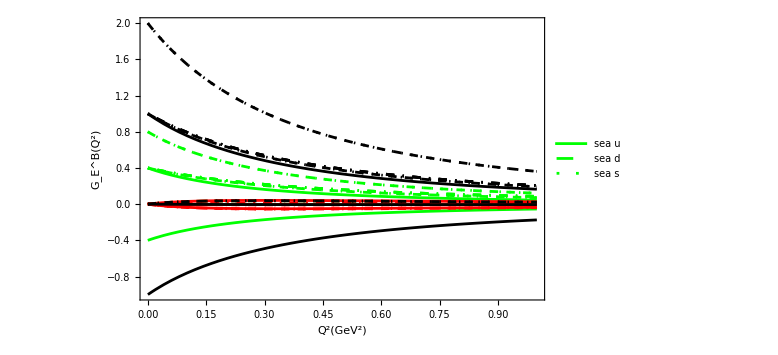

```mathematica
(*要作图的数据*)
norm=1;gegm=1;seva=5;;16;io=1;;3;
figAssoc["Data"]=figCalcInterval[[norm,gegm,seva,io]];
(*指定纵轴范围*)
figAssoc["PlotRange"]={{0,1},All};
(*指定图像空白填充范围，calc and expr 都生效*)
figAssoc["PlotRangePadding"]={{0,0},{Scaled[0.09],Scaled[0.12]}};
(*横纵坐标的标志*)
figAssoc["FrameLabel"]={
{Style["G_E^B(Q^2)",FontFamily->"Times New Roman",FontSize->frameText],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->frameText],None}
};
(*指定图例颜色，样式*)
figAssoc["LegendStyle"]=lineStyleTable⟦seva⟧;
(*指定图例文字*)
figAssoc["LegendText"]={"sea u","sea d","sea s"};
(*指定图例中符号的大小*)
figAssoc["LegendMarkerSize"]={28,2};
(*指定图例位置*)
figAssoc["LegendPositon"]={{0.85,0.7},(*锚点位置*){0,0}(*图的锚点*)};
figGroup[figAssoc]
```

## norm=2,gegm=1;seva=5;;8;io=1;

```mathematica
(*要作图的数据*)
norm=2;gegm=1;seva=5;;8;io=1;
figAssoc["Data"]=figCalcInterval[[norm,gegm,seva,io]];
(*指定纵轴范围*)
figAssoc["PlotRange"]={{0,1},All};
(*指定图像空白填充范围，calc and expr 都生效*)
figAssoc["PlotRangePadding"]={{0,0},{0,0}};
(*横纵坐标的标志*)
figAssoc["FrameLabel"]={
{Style["G_E^n(Q^2)",FontFamily->"Times New Roman",FontSize->frameText],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->frameText],None}
};
(*指定图例颜色，样式*)
figAssoc["LegendStyle"]=lineStyleTable⟦seva⟧;
(*指定图例文字*)
figAssoc["LegendText"]={"p","\!\(\*SuperscriptBox[\(Σ\), \(+\)]\)","\!\(\*SuperscriptBox[\(Σ\), \(-\)]\)"};
(*指定图例中符号的大小*)
figAssoc["LegendMarkerSize"]={28,2};
(*指定图例位置*)
figAssoc["LegendPositon"]={{0.04,0.65},(*锚点位置*){0,0}(*图的锚点*)};
```

## storage

```mathematica
echo["output directory"];(*将要导出的目录*)
outputDir=FileNameJoin[{gitLocalName,"/expression-results/"}]
echo["files to export"];(*要导出的文件,关联的形式，保存用的文件名->对应的文件*)
outputAssoc=<|
(*++++++++++++++++*)
FileNameJoin[{outputDir,"series."<>parOrderStr<>".ge.L-"<>parLambda0Str<>".ci-"<>parciStr<>".pdf"}]->aaa,
FileNameJoin[{outputDir,"series."<>parOrderStr<>".gm.L-"<>parLambda0Str<>".ci-"<>parciStr<>".pdf"}]->bbb
(*++++++++++++++++*)
|>;
echo["output status"];(*导出状态*)
KeyValueMap[Export,outputAssoc]
```